```mathematica
(* TECHNOLOGY PARAMETER FITTING *)

(* Clear everything *)
ClearAll["Global`*"]

(* Parameters: modify for each technology *)
fs=10^3;
techAParams={ρ->0.3*10^-6,Lmax->4*10^-9,wmax->50*10^-9,LT->1*10^-9,w0->0.5*10^-9,Rpar->2000,VT->0.4,I0->5*10^14,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->240*10^-6,γ->10^6,w1->1*10^-10,w2->1*10^-9};
techBParams={ρ->0.3*10^-6,Lmax->3*10^-9,wmax->50*10^-9,LT->0.5*10^-9,w0->0.5*10^-9,Rpar->5000,VT->0.4,I0->5*10^14,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->128*10^-6,γ->10^6,w1->1*10^-10,w2->1*10^-9};
techCParams={ρ->3*10^-6,Lmax->8*10^-9,LT->0.4*10^-9,w0->0.5*10^-9,Rpar->10000,VT->0.4,I0->10^13,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->50*10^-6,γ->10^12,w1->1*10^-10,w2->1*10^-9,n->10^3, Nlat->10, Nvert->1};
subs=techCParams;

(* Functions for conductance as a function of length and area in Stages 1 and 2 *)
g[A_,L_]:=(VT/(I0 A ⅇ^(-(Lmax-L)/LT))+(ρ L)/A+Rpar)^-1
gs1[L_]:=g[A0,L]
gs2[A_]:=g[A,Lmax]

(* Maximum conductance, length, area *)
Amax=InverseFunction[gs2][gmax]
A0=(π w0^2)/4
gtr=g[A0,Lmax]
gmax=gmax/.subs
Lmax=Lmax/.subs
Amax=InverseFunction[gs2][gmax]/.subs
w0=w0/.subs
A0/.subs

(* Show value for transition point between Stages 1 and 2 for conductance and volume *)
gtr*10^6/.subs

(4 VT)/(I0 π w0^2)/.subs
(4 Lmax ρ)/(π w0^2)/.subs
```

-(gmax (VT+I0 Lmax ρ))/(I0 (-1+gmax Rpar))

(π w0^2)/4

1/(Rpar+(4 VT)/(I0 π w0^2)+(4 Lmax ρ)/(π w0^2))

1/20000

1/125000000

6.4×10^-18

5.×10^-10

1.9635×10^-19

2.97664

203718.

122231.

```mathematica
(*Data=Import["E:\\Downloads\\RRAM-Relaxation-Master-Model-main\\techA_35hr_truncated.tsv"];*)
Data=Import["E:\\Downloads\\RRAM-Relaxation-Master-Model-main\\techA_35hr_modified.tsv"];
```

```mathematica
(*gt[Addr_,t_]:=
Module[{x},
x=Select[Data,#[[1]]==Addr&];
x[[First@Ordering[Abs[x[[All,2]]-t],1],4]]
]
Addr=DeleteDuplicates[Data[[All,1]]]
t={0,0.01,0.1,1,10,100000};*)

(* After preprocess, everything could be accessed directly through index instead of Select method *)
Addr=DeleteDuplicates[Data[[All,1]]];
Length[Addr]
t={0,0.01,0.1,1,10,100000};
gt[AddrCnt_,tCnt_]:=Data[[(AddrCnt-1)*Length[t]+tCnt,3]]
```

16292

```mathematica
(* Get range number, notice some initial conductance states exceed gmax *)
gmax0=40*^-6;
range=Min[#,31]&/@Quotient[gt[#,1]&/@Range[Length[Addr]],(gmax0/32)];
AddrList[n_]:=Flatten[Position[range,n]]
rangesPlot={0,8,16,24,31};
AddrPlot=AddrList[#]&/@rangesPlot;
```

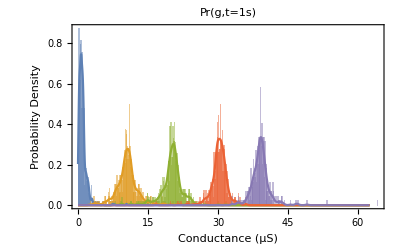

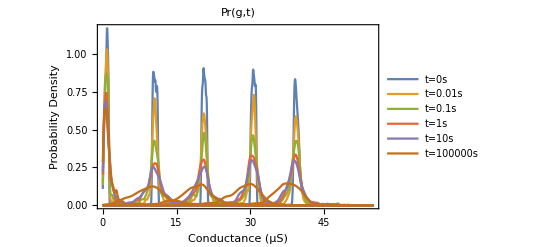

```mathematica
(* Plot conductance distributions at different times, each of the variables have Length[t] elements representing distributions of each time *)
gts=Table[gt[#,tCnt]&/@AddrPlot,{tCnt,Length[t]}];
gtdistKDEs=Table[Table[TruncatedDistribution[{0,gmax},SmoothKernelDistribution[gt,MaxMixtureKernels->All]],{gt,gts[[tCnt]]}],{tCnt,Length[t]}];
gtdistKDEpdfs=Table[Table[PDF[gtdistKDE,g],{gtdistKDE,gtdistKDEs[[tCnt]]}],{tCnt,Length[t]}];
scaled=gtdistKDEpdfs/10^6/.{g->x/10^6};
(* Plot PDF with histogram at t=1s *)
Show[Histogram[gts[[4]]*10^6,{0.1},"PDF",ChartStyle->ColorData[97,"ColorList"]],Plot[Evaluate@scaled[[4]],{x,0,gmax*10^6*1.25},PlotRange->All],PlotLabel->"Pr(g,t=1s)",Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
(* Plot as Fig. 13 *)
Show[Table[Plot[scaled[[tCnt]],{x,0,gmax*10^6*1.1},PlotRange->All,PlotStyle->ColorData[97,tCnt],PlotLegends->LineLegend[{"t="<>ToString[t[[tCnt]]]<>"s"}]],{tCnt,Length[t]}],PlotLabel->"Pr(g,t)",Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
```

```mathematica
Map[Variance,gtdistKDEs,{2}]
Clear[t]
```

{{1.00717×10^-13,1.32261×10^-13,1.3126×10^-13,1.30944×10^-13,1.08267×10^-12},{1.88092×10^-13,1.25985×10^-12,1.20719×10^-12,6.03656×10^-13,1.67662×10^-12},{5.72881×10^-13,3.12388×10^-12,3.5849×10^-12,2.2533×10^-12,2.16502×10^-12},{8.74028×10^-13,5.576×10^-12,6.09216×10^-12,3.31168×10^-12,3.3543×10^-12},{2.05906×10^-12,6.21017×10^-12,6.93319×10^-12,4.14652×10^-12,4.06523×10^-12},{1.3783×10^-12,1.49906×10^-11,1.46975×10^-11,1.22017×10^-11,1.03114×10^-11}}

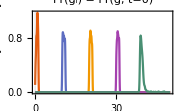

```mathematica
(*(* GENERATE INITIAL CONDUCTANCE DISTRIBUTIONS *)

(* Initial distribution settings *)
nranges=8;
gwidth=gmax/32;
gmeans=Range[gwidth/2,gmax,gmax/nranges];

(* Initial conductance distribution *)
gidists=Table[UniformDistribution[{gval-gwidth/2,gval+ gwidth/2}],{gval,gmeans}];
(*gidists=Table[NormalDistribution[gval,gwidth],{gval,gmeans}];*)
gidistpdfs=Table[PDF[gidist,g],{gidist,gidists}];*)
gidists=gtdistKDEs[[1,All]];
gidistpdfs=gtdistKDEpdfs[[1,All]];
scaled=gidistpdfs/10^6/.{g->x/10^6};
Plot[scaled,{x,0,gmax*10^6},PlotRange->All,PlotLabel->"Pr(g_i) = Pr(g, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
```

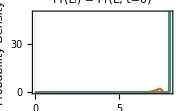

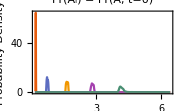

{6.59436×10^-20,6.4×10^-23,6.4×10^-23,6.4×10^-23,6.4×10^-23}

{3.84853×10^-41,8.7411×10^-40,1.47766×10^-39,2.40753×10^-39,5.24308×10^-38}

```mathematica
(* TRANSLATE CONDUCTANCE DISTRIBUTIONS TO AREA/LENGTH DISTRIBUTIONS *)

(* Use interpolation for inverse function, then sample and generate KDE *)
npts=1000;
nsamps=1000;

Off[General::munfl]
LDist[samps_]:=If[Variance[samps]>0,KernelMixtureDistribution[samps,MaxMixtureKernels->All],NormalDistribution[Mean[samps]-5*Lmax/npts,Lmax/npts]]
ADist[samps_]:=If[Variance[samps]>0,KernelMixtureDistribution[samps,MaxMixtureKernels->All],NormalDistribution[Mean[samps]+5*(Amax-A0)/npts,(Amax-A0)/npts]]

(* Length as function of conductance *)
gs1invpts=Table[{gs1[L]/.subs,L},{L,0,Lmax,Lmax/npts}];
PrependTo[gs1invpts,{0,0}];
AppendTo[gs1invpts,{gmax,Lmax}];
gs1inv=Interpolation[gs1invpts,InterpolationOrder->1]; 
(*Plot[gs1inv[g/10^6],{g,0,gmax*10^6},PlotRange->All]*)

(* Area as function of conductance *)
gs2invpts=Table[{gs2[A]/.subs,A},{A,A0,Amax,(Amax-A0)/npts}];
PrependTo[gs2invpts,{0,A0}];
gs2inv=Interpolation[gs2invpts,InterpolationOrder->1]; 

(* Length distribution *)
Lidists=Table[TransformedDistribution[gs1inv[g],g\[Distributed]gidist],{gidist,gidists}];
Lisamps=Table[RandomVariate[Lidist,nsamps],{Lidist,Lidists}];
LidistKDEs=Table[LDist[Lisamp],{Lisamp,Lisamps}];
LidistKDEpdfs=Table[PDF[LidistKDE,L],{LidistKDE,LidistKDEs}];
scaled=LidistKDEpdfs/10^9/.{L->x/10^9};
Plot[scaled,{x,0,Lmax*10^9},PlotRange->All,PlotLabel->"Pr(L_i) = Pr(L, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Initial Length (nm)",None}}]

(* Area distribution *)
Aidists=Table[TransformedDistribution[gs2inv[g],g\[Distributed]gidist],{gidist,gidists}];
Aisamps=Table[RandomVariate[Aidist,nsamps],{Aidist,Aidists}];
AidistKDEs=Table[ADist[Aisamp],{Aisamp,Aisamps}];
AidistKDEpdfs=Table[PDF[AidistKDE,A],{AidistKDE,AidistKDEs}];
scaled=AidistKDEpdfs/10^18/.{A->x/10^18};
Plot[scaled,{x,A0*10^18,Amax*10^18},PlotRange->All,PlotLabel->"Pr(A_i) = Pr(A, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Initial Area (nm^2)",None}}]

N@Map[Variance,LidistKDEs]
Map[Variance,AidistKDEs]
(*(* 3D plot *)
Pjoint=(LidistKDEpdfs/10^9/.{L->x/10^9})(AidistKDEpdfs/10^18/.{A->y/10^18});
Plot3D[Pjoint,{x,0,Lmax*10^9},{y,A0*10^18,Amax*10^18},PlotRange->All,PlotLabel->"Pr(A_i, L_i) = Pr(A, L, t=0)",Exclusions->None,PlotPoints->100,PlotTheme->"Scientific",AxesLabel->{"Length (nm)", "Area (nm^2)", "Prob. Density"}]*)
```

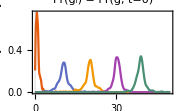

```mathematica
gfexactdists=gtdistKDEs[[4,All]];
gfexactdistpdfs=gtdistKDEpdfs[[4,All]];
scaled=gfexactdistpdfs/10^6/.{g->x/10^6};
Plot[scaled,{x,0,gmax*10^6},PlotRange->All,PlotLabel->"Pr(g_i) = Pr(g, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
```

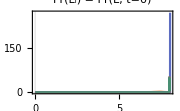

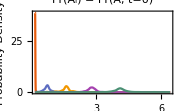

{1.46933×10^-19,4.53356×10^-23,6.4×10^-23,6.4×10^-23,6.4×10^-23}

{2.06259×10^-39,3.86562×10^-38,6.49121×10^-38,5.42268×10^-38,1.27993×10^-37}

```mathematica
(* Use interpolation for inverse function, then sample and generate KDE *)
npts=1000;
nsamps=1000;

Off[General::munfl]

(* Length distribution *)
Lfexactdists=Table[TransformedDistribution[gs1inv[g],g\[Distributed]gfexactdist],{gfexactdist,gfexactdists}];
Lfexactsamps=Table[RandomVariate[Lfexactdist,nsamps],{Lfexactdist,Lfexactdists}];
LfexactdistKDEs=Table[LDist[Lfexactsamp],{Lfexactsamp,Lfexactsamps}];
LfexactdistKDEpdfs=Table[PDF[LfexactdistKDE,L],{LfexactdistKDE,LfexactdistKDEs}];
scaled=LfexactdistKDEpdfs/10^9/.{L->x/10^9};
Plot[scaled,{x,0,Lmax*10^9},PlotRange->All,PlotLabel->"Pr(L_i) = Pr(L, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Initial Length (nm)",None}}]

(* Area distribution *)
Afexactdists=Table[TransformedDistribution[gs2inv[g],g\[Distributed]gfexactdist],{gfexactdist,gfexactdists}];
Afexactsamps=Table[RandomVariate[Afexactdist,nsamps],{Afexactdist,Afexactdists}];
AfexactdistKDEs=Table[ADist[Afexactsamp],{Afexactsamp,Afexactsamps}];
AfexactdistKDEpdfs=Table[PDF[AfexactdistKDE,A],{AfexactdistKDE,AfexactdistKDEs}];
scaled=AfexactdistKDEpdfs/10^18/.{A->x/10^18};
Plot[scaled,{x,A0*10^18,Amax*10^18},PlotRange->All,PlotLabel->"Pr(A_i) = Pr(A, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Initial Area (nm^2)",None}}]

varfexactL=N@Map[Variance,LfexactdistKDEs]
varfexactA=N@Map[Variance,AfexactdistKDEs]
```

(8.79523×10^-18 Nvert^2)/((-Ea1+Ea2)/kT+(-w1+w2) γ)

-(4.39761×10^-18 kT Nvert^2)/(Ea1-1. Ea2+kT (w1-1. w2) γ)

4.88624×10^-21

1/200000000000000000000

(5.29818×10^-39 Nlat^2)/((-Ea1+Ea2)/kT+(-w1+w2) γ)

-(2.64909×10^-39 kT Nlat^2)/(Ea1-1. Ea2+kT (w1-1. w2) γ)

2.94343×10^-40

1/5000000000000000000000000000000000000000

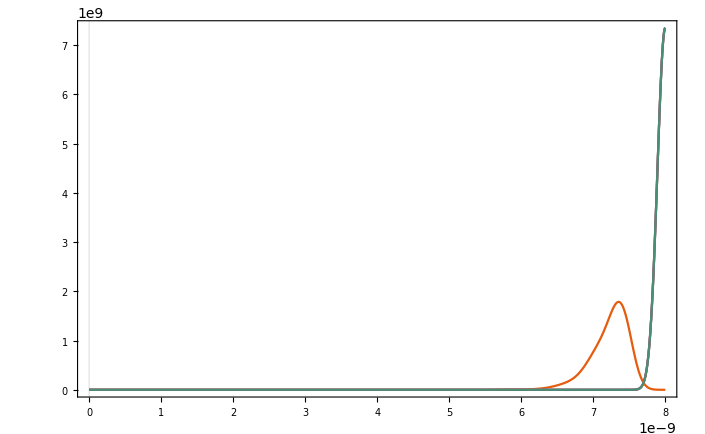

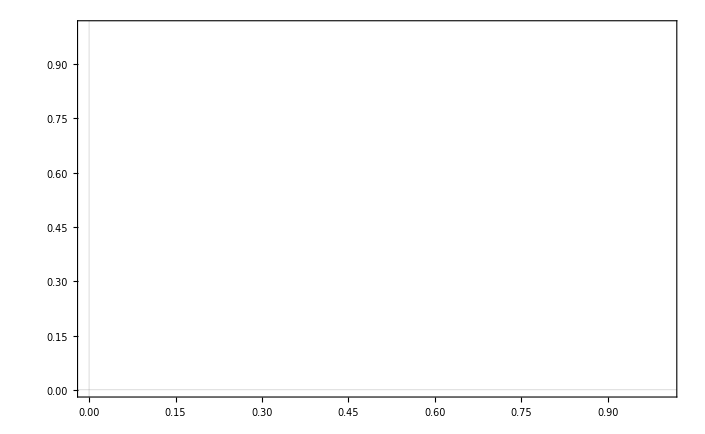

```mathematica
(* SOLVE FOR FINAL LENGTH/AREA DISTRIBUTIONS *)

(* Mesh points setting *)
meshpts=1000;

(* Final time to solve for *)
tf=1;

(* Compute constants *)
varL=((Nvert w0^3)/A0 )^2(π Log[fs tf])/((Ea2 - Ea1)/kT + γ(w2-w1))
DiffL=Simplify[PowerExpand[varL/(2tf)]]
N[DiffL/.subs]
DiffL=5*10^-21

varA=((Nlat w0^3)/Lmax )^2(π Log[fs tf])/((Ea2 - Ea1)/kT + γ(w2-w1))
DiffA=Simplify[PowerExpand[varA/(2tf)]]
N[DiffA/.subs]
DiffA=2*10^-40

(* Solve diffusion equation for length with initial/boundary conditions *)
method={"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->Lmax/meshpts}}}};
heqn=D[p[L,t],t]-D[DiffL p[L,t],{L,2}]==NeumannValue[0,L==0]+NeumannValue[0,L==Lmax];
ics=Table[p[L,0]==icfn,{icfn,LidistKDEpdfs}];
Lfpdfs=p[L,tf]/.Table[NDSolve[{heqn/.subs,ic},p[L,tf],{L,0,Lmax},{t,0,tf},InterpolationOrder->All,Method->method],{ic,ics}];
Plot[Lfpdfs,{L,0,Lmax},PlotRange->All,PlotTheme->"Scientific"]

(* Solve diffusion equation for area with initial/boundary conditions *)
method={"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->(Amax-A0)/meshpts}}}};
heqn=D[p[A,t],t]-D[DiffA p[A,t],{A,2}]==NeumannValue[0,A==A0]+NeumannValue[0,A==Amax];
ics=Table[p[A,0]==icfn,{icfn,AidistKDEpdfs}];
Afpdfs=p[A,tf]/.Table[NDSolve[{heqn/.subs,ic},p[A,tf],{A,A0,Amax},{t,0,tf},InterpolationOrder->All,Method->method],{ic,ics}];
Plot[Afpdfs,{A,A0,Amax},PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
Table[NIntegrate[A^2 Abs[Afpdf[[1]]],{A,A0,Amax},MaxRecursion->15]-(NIntegrate[A Abs[Afpdf[[1]]],{A,A0,Amax},MaxRecursion->15])^2,{Afpdf,Afpdfs}]
varfexactA
Table[NIntegrate[L^2 Abs[Lfpdf[[1]]],{L,0,Lmax},MaxRecursion->15]-(NIntegrate[L Abs[Lfpdf[[1]]],{L,0,Lmax},MaxRecursion->15])^2,{Lfpdf,Lfpdfs}]
varfexactL
```

{3.57436×10^-40,1.27406×10^-39,1.87772×10^-39,2.82178×10^-39,5.28423×10^-38}

{2.06259×10^-39,3.86562×10^-38,6.49121×10^-38,5.42268×10^-38,1.27993×10^-37}

{7.59513×10^-20,4.23087×10^-21,4.23087×10^-21,4.23087×10^-21,4.23087×10^-21}

{1.46933×10^-19,4.53356×10^-23,6.4×10^-23,6.4×10^-23,6.4×10^-23}

```mathematica
(* TRANSLATE LENGTH/AREA DISTRIBUTIONS BACK TO CONDUCTANCE DISTRIBUTIONS *)
npts=1000;
Table[NIntegrate[Abs[Afpdf[[1]]],{A,A0,Amax},MaxRecursion->15],{Afpdf,Afpdfs}]
Table[NIntegrate[Abs[Lfpdf[[1]]],{L,0,Lmax},MaxRecursion->15],{Lfpdf,Lfpdfs}]
wfdists=ParallelTable[ProbabilityDistribution[Abs[Afpdf[[1]]],{A,A0,Amax},Method->"Normalize"],{Afpdf,Afpdfs}];
Lfdists=ParallelTable[ProbabilityDistribution[Abs[Lfpdf[[1]]],{L,0,Lmax},Method->"Normalize"],{Lfpdf,Lfpdfs}];
(*gfdists=MapThread[TransformedDistribution[g[A,L],{A\[Distributed]#1,L\[Distributed]#2}]&,{wfdists,Lfdists}]*)
gfdists=ParallelMap[TransformedDistribution[g[A,L],{A\[Distributed]#1,L\[Distributed]#2}]&@@#&,{wfdists,Lfdists}//Transpose]
```

{0.999999,1.,1.,0.999998,0.999999}

{1.,1.,1.,1.,1.}

{TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 6.4 10   }, {0., 1.}}, <>][x,1]],{x,1.9635×10^-19,6.4×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1.}}, <>][x,1]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[0.99999 Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 6.4 10   }, {0., 1.}}, <>][x,1]],{x,1.9635×10^-19,6.4×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1.}}, <>][x,1]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 6.4 10   }, {0., 1.}}, <>][x,1]],{x,1.9635×10^-19,6.4×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1.}}, <>][x,1]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 6.4 10   }, {0., 1.}}, <>][x,1]],{x,1.9635×10^-19,6.4×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1.}}, <>][x,1]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((1/125000000-L)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19        -18
InterpolatingFunction[{{1.9635 10   , 6.4 10   }, {0., 1.}}, <>][x,1]],{x,1.9635×10^-19,6.4×10^-18}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 1.}}, <>][x,1]],{x,0,1/125000000}]}]}

```mathematica
(* SAMPLE FINAL CONDUCTANCE DISTRIBUTIONS AND CREATE PDF *)
nsamps=1000;
gfsamps=ParallelTable[RandomVariate[gfdist/.subs,nsamps],{gfdist,gfdists}] ;
gfdistKDEs=ParallelTable[SmoothKernelDistribution[gfsamp,MaxMixtureKernels->All],{gfsamp,gfsamps}];
gfdistKDEpdfs=ParallelTable[PDF[gfdistKDE,g],{gfdistKDE,gfdistKDEs}];
(*data=Transpose[{gfdistKDEpdfs,gidistpdfs}];*)
```

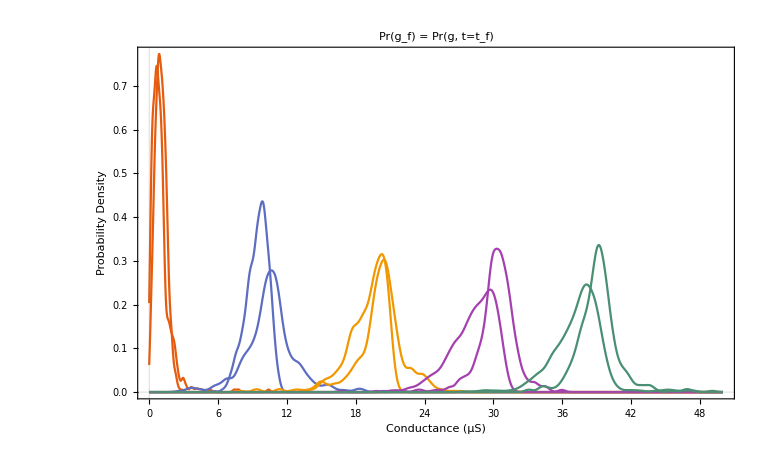

```mathematica
(* PLOT FINAL CONDUCTANCE DISTRIBUTIONS *)

(* Final conductance distributions *)
scaled=Transpose[{gfdistKDEpdfs,gfexactdistpdfs}]/10^6/.{g->x/10^6};
(*scaled=gfdistKDEpdfs/10^6/.{g->x/10^6};*)
Plot[scaled,{x,0,gmax*10^6},PlotRange->All,PlotLabel->"Pr(g_f) = Pr(g, t=t_f)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]

(* Plot final joint area/length probability distribution *)

(* 3D plot *)
(*Pjoint=(Lfpdfs/10^9/.{L->x/10^9})(Afpdfs/10^18/.{A->y/10^18});
Plot3D[Pjoint,{x,0,Lmax*10^9},{y,A0*10^18,Amax*10^18},PlotRange->All,PlotLabel->"Pr(A_f, L_f) = Pr(A, L, t=t_f)",Exclusions->None,PlotPoints->100,PlotTheme->"Scientific"]*)
```

```mathematica
Map[Variance,gfdistKDEs]
Map[Variance,gtdistKDEs,{2}][[4]]
```

{1.9142×10^-13,1.03733×10^-12,2.73176×10^-12,5.03634×10^-12,8.24367×10^-12}

{8.74028×10^-13,5.576×10^-12,6.09216×10^-12,3.31168×10^-12,3.3543×10^-12}